```mathematica
filename[k_]:=If[k<1501,Import["/home/andrea/Downloads/N250_k1_5/data/out/x/x0_mt_g"<>ToString[k]<>".dat","CSV"]]
```

```mathematica
filename2[k_]:=If[k<1501,"con_mt_N2500_g"<>ToString[k]<>".jpg"]
```

```mathematica
grafico[T_] :=(
Show[ListLogLogPlot[ReverseSort[filename[k][[1]]],AxesLabel->{Index,Concentration}],LogLogPlot[ 0.2x^-1,{x,1,1000},PlotStyle->Green]]);
```

```mathematica
Do[Export[filename2[k], grafico[k],  "jpg"], {k, 1, 1500}]
```

```mathematica
gen98=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/x0_mt_g98.dat","CSV"];
```

```mathematica
gen87=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/x0_mt_g87.dat","CSV"];
gen78=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/x0_mt_g78.dat","CSV"];
```

```mathematica
gen99=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/x0_mt_g99.dat","CSV"];
```

```mathematica
gen150=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/x0_mt_g150.dat","CSV"];
gen220=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/x0_mt_g220.dat","CSV"];
```

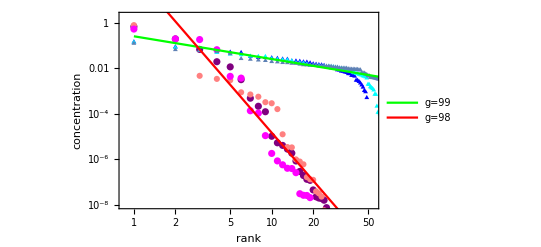

```mathematica
sgen0=Show[ListLogLogPlot[ReverseSort[gen98[[1]]],AxesLabel->{Style[rank,Italic],Style[concentration,Italic]},PlotStyle->Purple,PlotRange->{{0,55},{0.00000001,2}}, Frame->True],ListLogLogPlot[ReverseSort[gen99[[1]]],PlotMarkers->{▲,2.5},PlotStyle->Blue],ListLogLogPlot[ReverseSort[gen150[[1]]],PlotMarkers->{▲,2.5},PlotStyle->Cyan],ListLogLogPlot[ReverseSort[gen220[[1]]],PlotMarkers->{▲,2.5}],ListLogLogPlot[ReverseSort[gen78[[1]]],PlotStyle->Pink],ListLogLogPlot[ReverseSort[gen87[[1]]],PlotStyle->Magenta],LogLogPlot[0.26x^-1,{x,1,60},PlotStyle->Green,PlotLegends->{Style["g=99",Italic]}],LogLogPlot[150x^-7,{x,1,60},PlotStyle->Red,PlotLegends->{Style["g=98",Italic]}]]
```

```mathematica
Export["fig3.svg",sgen0]
```

fig3.svg

```mathematica
Clear[g]
```

```mathematica
ef=Import["/home/andrea/Downloads/dif_N1000_graph2_ef.dat","Table"];
```

```mathematica
inef=Import["/home/andrea/Downloads/dif_N1000_graph2_inef.dat","Table"];
```

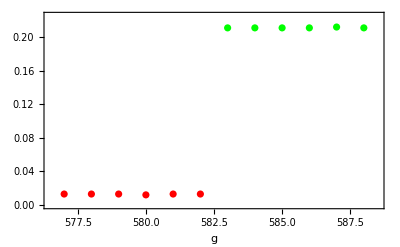

```mathematica
fig2=Show[ListPlot[inef,Frame->True,PlotStyle->Red,AxesLabel->{g},PlotRange->{{576.5,588.5},{0,0.225}}], ListPlot[ef, PlotStyle->Green]]
```

```mathematica
Export["fig2.svg",fig2]
```

fig2.svg

```mathematica
equp98=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_up_g98.dat","Table"];
equp98log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_up_g98_log.dat","Table"];
```

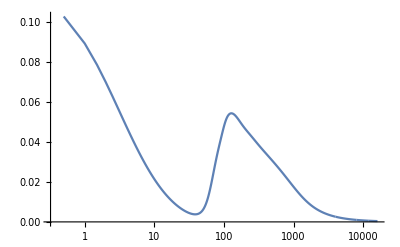

```mathematica
ListLogLinearPlot[{equp98},PlotRange->All,Joined->True]
```

```mathematica
equp99=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_up_g99.dat","Table"];
equp99log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_up_g99_log.dat","Table"];
```

```mathematica
eq198=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq1_g98.dat","Table"];
eq198log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq1_g98_log.dat","Table"];
```

```mathematica
eq199=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq1_g99.dat","Table"];
eq199log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq1_g99_log.dat","Table"];
```

```mathematica
eq3098=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq30_g98.dat","Table"];
eq3098log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq30_g98_log.dat","Table"];
```

```mathematica
eq3099=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq30_g99.dat","Table"];
eq3099log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq30_g99_log.dat","Table"];
```

```mathematica
eqgrad98=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_grad_g98.dat","Table"];
eqgrad98log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_grad_g98_log.dat","Table"];
```

```mathematica
eqgrad99=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_grad_g99.dat","Table"];
eqgrad99log=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/x/equilibrium/eq_grad_g99_log.dat","Table"];
```

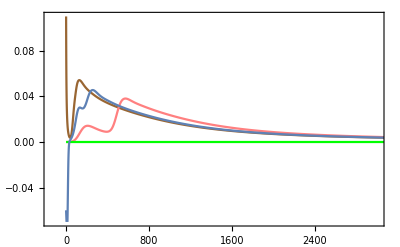

```mathematica
fig4a=Show[ListLinePlot[equp98,Frame->True,PlotStyle->Brown,PlotRange->{{-150,3005},{-0.07,0.11}}],  ListLinePlot[eq3098,PlotStyle->Pink,PlotRange->{{-50,3005},{-0.07,0.11}}],ListLinePlot[eqgrad98,PlotStyle->Green,PlotRange->{{-50,3005},{-0.07,0.11}}],ListLinePlot[eq198,PlotRange->{{-50,3005},{-0.07,0.11}}]]
```

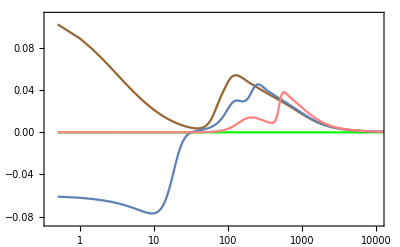

```mathematica
fig4alog=Show[ListLogLinearPlot[eqgrad98,PlotStyle->Green,PlotRange->{{0.4,10500},{-0.085,0.11}},Joined->True,Frame->True],ListLogLinearPlot[equp98,Frame->True,PlotStyle->Brown,PlotRange->All,Joined->True],ListLogLinearPlot[eq198,PlotRange->All,Joined->True],ListLogLinearPlot[eq3098,Frame->True,PlotStyle->Pink,PlotRange->All,Joined->True]]
```

```mathematica
Export["fig4alog.svg",fig4alog]
```

fig4alog.svg

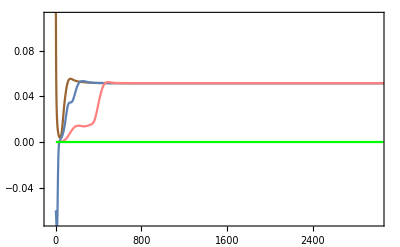

```mathematica
fig4b=Show[ListLinePlot[equp99,Frame->True,PlotStyle->Brown],  ListLinePlot[eq199],ListLinePlot[eq3099,PlotStyle->Pink],ListLinePlot[eqgrad99,PlotStyle->Green], PlotRange->{{-50,3005},{-0.07,0.11}}]
```

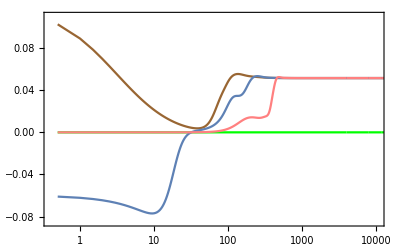

```mathematica
fig4blog=Show[ListLogLinearPlot[eqgrad99,PlotStyle->Green,PlotRange->{{0.4,10500},{-0.085,0.11}},Joined->True,Frame->True,PlotStyle->Thickness],ListLogLinearPlot[equp99,Frame->True,PlotStyle->Brown,PlotRange->All,Joined->True],ListLogLinearPlot[eq199,PlotRange->All,Joined->True],ListLogLinearPlot[eq3099,Frame->True,PlotStyle->Pink,PlotRange->All,Joined->True]]
```

```mathematica
Export["fig4b.svg",fig4blog]
```

fig4b.svg

```mathematica
gcomp=Import["/home/andrea/Downloads/gcomp_8-05.dat","Table"];
```

```mathematica
gcomp2=Import["/home/andrea/Downloads/N250/N250_k1_6/data/out/grafo funcional/nodes_gcomp_4105.dat","Table"];
```

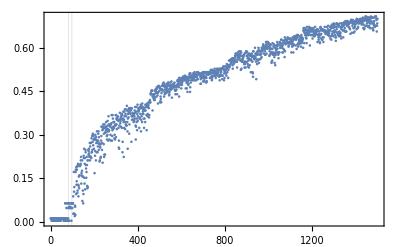

```mathematica
fig1=Show[ListPlot[gcomp2,Frame->True],GridLines->{{82,98},{}},GridLinesStyle->{{Gray, Dashed},{Red, Dashed}}]
```

```mathematica
Export["fig1_N250.svg",fig1]
```

fig1_N250.svg